## Notebook Setup

## Pre-amble

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

Inversions::shdw: Symbol Inversions appears in multiple contexts {Combinatorica`,Global`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
```

## An Introduction to Q-Analysis - Warren P. Johnson

## Chapter 1. Inversions

### 1.1 Stern’s Problem

#### Definition: Inversion

Inversion is a concept in discrete mathematics to measure how much a sequence is out of its natural order.
Definition Inversion: Let p = p_1 p_2... p_n be a permutation. We say that (p_i, p_j) is an inversion of p if i < j but p_i > p_j. 
Example: In the permutation {1,3,2}  (p_2,p_3) is an inversion of {1,3,2} since 2 < 3 but p_2 > p_3. ( 3 > 2 ).
The element-based inversion set is essentially the place-based inversion set of the inverse permutation, just with the elements of the pairs exchanged.

#### Formula: Total number of inversions of permutations of length n

I_n= n I_(n-1)+ (n-1)! (n
2)

```mathematica
RSolve[{a[1]==0,a[n]==n a[n-1]+(n-1)!Binomial[n,2]},a[n],n]
```

{{a[n]→1/4 (-1+n) n Pochhammer[1,n]}}

```mathematica
g[n_]:=1/4 (-1+n) n Pochhammer[1,n]
Table[{x,x!,g[x],g[x]/x!,2g[x]/x!},{x,1,12,1}]//TableForm
```

1 | 1 | 0 | 0 | 0
2 | 2 | 1 | 1/2 | 1
3 | 6 | 9 | 3/2 | 3
4 | 24 | 72 | 3 | 6
5 | 120 | 600 | 5 | 10
6 | 720 | 5400 | 15/2 | 15
7 | 5040 | 52920 | 21/2 | 21
8 | 40320 | 564480 | 14 | 28
9 | 362880 | 6531840 | 18 | 36
10 | 3628800 | 81648000 | 45/2 | 45
11 | 39916800 | 1097712000 | 55/2 | 55
12 | 479001600 | 15807052800 | 33 | 66

#### Theorem: Rothe’s Theorem on Conjugate permutations

Conjugate permutations have the same number of inversions

Example:

```mathematica
p={4,5,1,3,2,6};
Inversions[p]
Inversions[InversePermutation[p]]
```

7

7

### 1.2 The q-Factorial

#### Definition: the q-Analogue of the number n

```mathematica
nQAnalogue2[n_]:=Total[Table[q^k,{k,0,n-1}]]
nQAnalogue1[n_]:=Simplify[(1-q^n)/(1-q)]
nQAnalogue[n_]:=Series[(1-q^n)/(1-q),{q,0,50}]//Normal
Table[{k,nQAnalogue[k]},{k,10,30,10}]//TableForm
```

10 | 1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9
20 | 1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12+q^13+q^14+q^15+q^16+q^17+q^18+q^19
30 | 1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12+q^13+q^14+q^15+q^16+q^17+q^18+q^19+q^20+q^21+q^22+q^23+q^24+q^25+q^26+q^27+q^28+q^29

#### Definition: the q-Analogue of n!

```mathematica
Series[QFactorial[4,q],{q,0,10}]//Normal
```

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

```mathematica
nQAnalogue[1]nQAnalogue[2]nQAnalogue[3]//Expand 
nQAnalogue[1]nQAnalogue[2]nQAnalogue[3]nQAnalogue[4]//Expand
```

1+2 q+2 q^2+q^3

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

```mathematica
-q^-4 nQAnalogue[4]
nQAnalogue[-4]
(1-q^-4)/(1-q)//Simplify
```

-(1+q+q^2+q^3)/q^4

-1/q^4-1/q^3-1/q^2-1/q

-(1+q+q^2+q^3)/q^4

```mathematica
nQAnalogue[9]
nQAnalogue[3]+q^3 nQAnalogue[6]//Simplify
```

1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8

1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8

```mathematica
nQAnalogue[5]nQAnalogue[5]//Expand
```

1+2 q+3 q^2+4 q^3+5 q^4+4 q^5+3 q^6+2 q^7+q^8

#### Theorem: Rodrigues’s theorem.

### 1.3 q-Binomial Coefficients

### 1.4 Some identities for q-binomial coefficients

### 1.5 Another property of q-binomial coefficients

## Temp

```mathematica
Series[QPochhammer[q],{q,0,20}]//Normal
```

1-q-q^2+q^5+q^7-q^12-q^15

```mathematica
nQAnalogue[7]
nQAnalogue[3]+q^3 nQAnalogue[4]//Simplify
```

1+q+q^2+q^3+q^4+q^5+q^6

1+q+q^2+q^3+q^4+q^5+q^6

```mathematica
nQAnalogue[3]nQAnalogue[3]//Expand
nQAnalogue[3]nQAnalogue[3]//Expand
```

1+2 q+3 q^2+2 q^3+q^4

1+2 q+3 q^2+2 q^3+q^4

```mathematica
nQAnalogue[4]nQAnalogue[2]//Expand
nQAnalogue[5]nQAnalogue[2]//Expand
nQAnalogue[6]nQAnalogue[2]//Expand
nQAnalogue[7]nQAnalogue[2]//Expand
```

1+2 q+2 q^2+2 q^3+q^4

1+2 q+2 q^2+2 q^3+2 q^4+q^5

1+2 q+2 q^2+2 q^3+2 q^4+2 q^5+q^6

1+2 q+2 q^2+2 q^3+2 q^4+2 q^5+2 q^6+q^7

```mathematica
nQAnalogue[4]nQAnalogue[3]//Expand
nQAnalogue[5]nQAnalogue[3]//Expand
nQAnalogue[6]nQAnalogue[3]//Expand
nQAnalogue[7]nQAnalogue[3]//Expand
```

1+2 q+3 q^2+3 q^3+2 q^4+q^5

1+2 q+3 q^2+3 q^3+3 q^4+2 q^5+q^6

1+2 q+3 q^2+3 q^3+3 q^4+3 q^5+2 q^6+q^7

1+2 q+3 q^2+3 q^3+3 q^4+3 q^5+3 q^6+2 q^7+q^8

```mathematica
nQAnalogue[7]nQAnalogue[5]//Expand
```

1+2 q+3 q^2+4 q^3+5 q^4+5 q^5+5 q^6+4 q^7+3 q^8+2 q^9+q^10

## Combinatorics of Permutations - Miklós Bóna

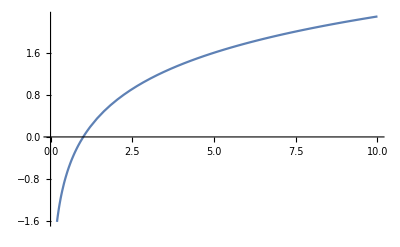

```mathematica
Plot[Log[x],{x,0,10},AxesOrigin->{0,0}]
```

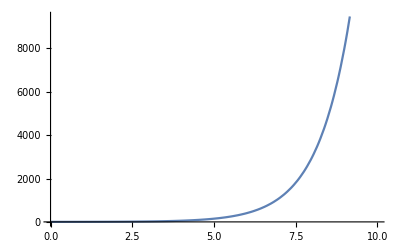

```mathematica
Plot[Exp[x],{x,0,10},AxesOrigin->{0,0}]
```